# Problem set 3.1

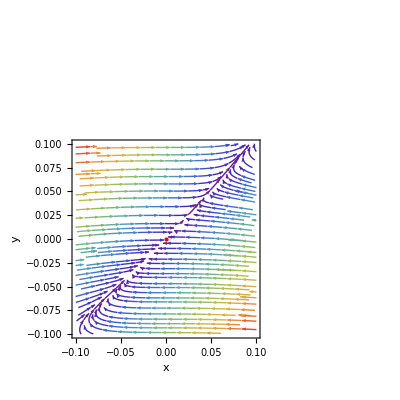

```mathematica
StreamPlot[{y - x, x^2}, {x, -0.1, 0.1}, {y, -0.1, 0.1}, 
	StreamStyle -> Automatic, 
	StreamColorFunction -> "Rainbow", 
	FrameLabel -> {"x", "y"}, 
	StreamPoints -> Fine,
	Epilog -> {
	Red, PointSize[Large], Point[{0, 0}],
	Black,
	Text[Style["Fixed-Point", 14, Bold], {0.5, 0.5}]
	},
	AspectRatio -> 1]
```

1

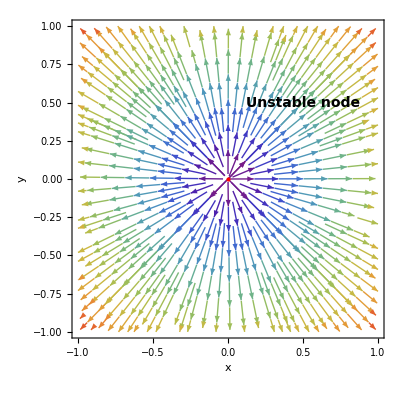

-1

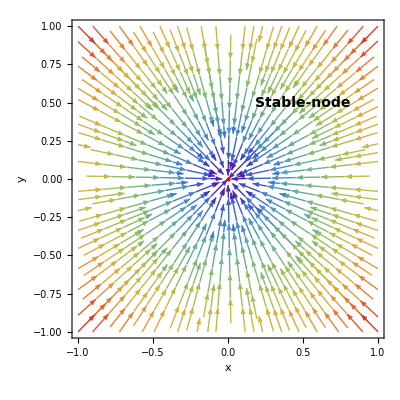

```mathematica
a = 1
StreamPlot[{a*x, a*y}, {x, -1, 1}, {y, -1, 1}, 
	StreamStyle -> Automatic, 
	StreamColorFunction -> "Rainbow", 
	FrameLabel -> {"x", "y"}, 
	StreamPoints -> Fine,
	Epilog -> {
	Red, PointSize[Large], Point[{0, 0}],
	Black,
	Text[Style["Unstable node", 14, Bold], {0.5, 0.5}]
	},
	AspectRatio -> 1]
	
a = -1
StreamPlot[{a*x, a*y}, {x, -1, 1}, {y, -1, 1}, 
	StreamStyle -> Automatic, 
	StreamColorFunction -> "Rainbow", 
	FrameLabel -> {"x", "y"}, 
	StreamPoints -> Fine,
	Epilog -> {
	Red, PointSize[Large], Point[{0, 0}],
	Black,
	Text[Style["Stable-node", 14, Bold], {0.5, 0.5}]
	},
	AspectRatio -> 1]
```

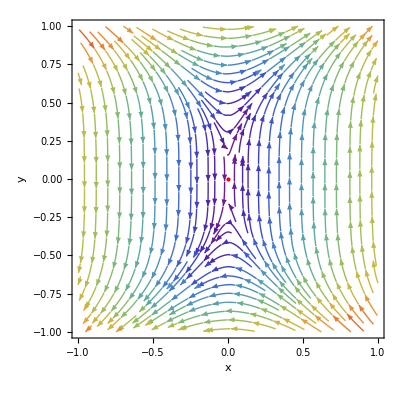

```mathematica
StreamPlot[{y^3, x}, {x, -1, 1}, {y, -1, 1}, 
	StreamStyle -> Automatic, 
	StreamColorFunction -> "Rainbow", 
	FrameLabel -> {"x", "y"}, 
	StreamPoints -> Fine,
	Epilog -> {
	Red, PointSize[Large], Point[{0, 0}],
	Black,
	Text[Style["", 14, Bold], {0.5, 0.5}]
	},
	AspectRatio -> 1]
```

3

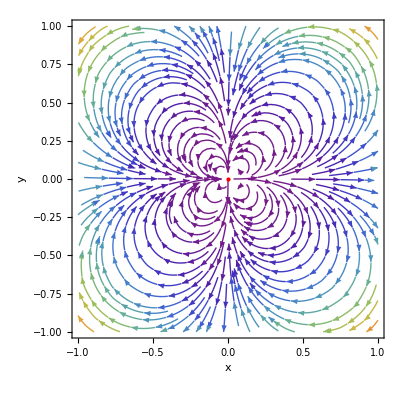

-3

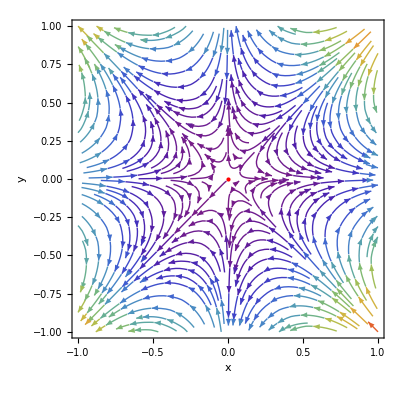

```mathematica
n = 3
StreamPlot[{(y^2+x^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]], (y^2+x^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]]}, {x, -1, 1}, {y, -1, 1}, 
	StreamStyle -> Automatic, 
	StreamColorFunction -> "Rainbow", 
	FrameLabel -> {"x", "y"}, 
	StreamPoints -> Fine,
	Epilog -> {
	Red, PointSize[Large], Point[{0, 0}],
	Black,
	Text[Style["", 14, Bold], {0.5, 0.5}]
	},
	AspectRatio -> 1]
n = -3
StreamPlot[{(y^2+x^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]], (y^2+x^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]]}, {x, -1, 1}, {y, -1, 1}, 
	StreamStyle -> Automatic, 
	StreamColorFunction -> "Rainbow", 
	FrameLabel -> {"x", "y"}, 
	StreamPoints -> Fine,
	Epilog -> {
	Red, PointSize[Large], Point[{0, 0}],
	Black,
	Text[Style["", 14, Bold], {0.5, 0.5}]
	},
	AspectRatio -> 1]
```